```mathematica
(* matrix Subscript[T, 8]^(1)(x) *)
(* 2018-02-24 W. Bruzda (improved with help of referee) *)
(* see also: T8_1.m script *)
```

```mathematica
(* constants *)
Subscript[ζ, 1]=Root[80+20 #1^2+#1^4&,1];
Subscript[ζ, 2]=Root[80+20 #1^2+#1^4&,2];
Subscript[ζ, 3]=Root[80+20 #1^2+#1^4&,3];
Subscript[ζ, 4]=Root[80+20 #1^2+#1^4&,4];
```

```mathematica
(* draw a free parameter at random *)
(* x = x(γ) : γ (phase) must be within a particular range so that the other entries remain unimodular *)

(* x = -0.9481448970234081-0.31783840902016647 ⅈ; 
first try for a = 0.551478475784210 - see: T8.nb (2018-01-01) *)

x1=Exp[I Pi Random[Real,{0.38629047387009,0.8301134750001507}]];
x2=Exp[I Pi Random[Real,{0.9700212764097545,1.413709525400110}]];
t=Random[Integer];
(* take either of two branches... *)
x=t*x1 +(1-t)*x2
```

-0.298309+0.954469 ⅈ

```mathematica
(* get T8 = T8(x) with y = y(x), z = z(x), u = u(x) *)
Subscript[χ, 1]=5-3 √5+4 √(5-2 √5)+(1+I) 1/x+Subscript[ζ, 2];
Subscript[χ, 2]=45-9 I-(17-7 I) √5-2 √(620-500 I-(285-234 I) √5)-(1+I) Subscript[χ, 1]/x;
Subscript[χ, 3]=10 I-10+(6-2 I) √5+4 √(10-10 ⅈ-(5-4 ⅈ) √5)+(1+I) Subscript[χ, 2]/x;
Subscript[χ, 4]=√5-1+I √2 √(5+√5)+(1+I) Subscript[χ, 3]/x;
Subscript[χ, 5]=(1+I) √(1-√5+Subscript[ζ, 4])-(1-I)( 2 x^2+Conjugate[√Subscript[χ, 4]])-x (1-4 I+√5+Subscript[ζ, 1]);
Subscript[χ, 6]=√5-1-I-√(5-2 √5)+(1- I) x;
y=1/4 Subscript[χ, 5]/Subscript[χ, 6];
z=x/(x-y)((1+I) (-1)^(4/5)-x-y-1+I);
u=I/z(x^2-z x + x y + y z)/(1+I-(-1)^(3/10)-(-1)^(4/5));
T=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 3, 15, 18}, {0, 8, 8, 8, 8, 13, 15, 8}, {0, 2, 2, 2, 2, 17, 5, 2}, {0, 0, 0, 0, 0, 7, 5, 12}, {0, 0, 0, 0, 0, 0, 10, 10}, {0, 0, 0, 0, 0, 10, 0, 10}, {0, 0, 0, 0, 0, 10, 10, 0}});
T8=Exp[I Pi T 1/10]*({{1, 1, 1, 1, 1, 1, 1, 1}, {1, x, y, z, -(y z)/x, 1, 1, 1}, {1, -u/y, u/x, -(u z)/(x y), -(u z)/x^2, 1, 1, 1}, {1, y, x, -(y z)/x, z, 1, 1, 1}, {1, u/x, -u/y, -(u z)/x^2, -(u z)/(x y), 1, 1, 1}, {1, -I x/z, I x/z, -I z/x, I z/x, 1, 1, 1}, {1, u, -u, -(u z^2)/x^2, (u z^2)/x^2, 1, 1, 1}, {1, I(u z)/x, I(u z)/x, -I(u z)/x, -I(u z)/x, 1, 1, 1}});
```

```mathematica
(* due to the construction Arg[u]/2./Pi should be in [-0.5, 0.5] *)
Arg[u]/2./Pi
T8//MatrixForm//N//Chop
```

0.18295

(1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | -0.298309+0.954469 ⅈ | -0.997581+0.0695096 ⅈ | -0.370919-0.928665 ⅈ | -0.729993+0.683454 ⅈ | 0.587785+0.809017 ⅈ | 0.-1. ⅈ | 0.809017-0.587785 ⅈ
1. | -0.830519-0.55699 ⅈ | -0.216542+0.976273 ⅈ | 0.995756-0.0920313 ⅈ | 0.448108+0.89398 ⅈ | -0.587785-0.809017 ⅈ | 0.-1. ⅈ | -0.809017+0.587785 ⅈ
1. | -0.847917-0.530129 ⅈ | -0.80236+0.596841 ⅈ | -0.992301+0.123847 ⅈ | 0.245776-0.969327 ⅈ | 0.587785-0.809017 ⅈ | 0.+1. ⅈ | 0.809017+0.587785 ⅈ
1. | 0.749025-0.662541 ⅈ | 0.344514+0.938781 ⅈ | 0.162941-0.986636 ⅈ | -0.859678-0.510836 ⅈ | -0.587785+0.809017 ⅈ | 0.+1. ⅈ | -0.809017-0.587785 ⅈ
1. | -0.63106+0.775734 ⅈ | 0.63106-0.775734 ⅈ | 0.63106+0.775734 ⅈ | -0.63106-0.775734 ⅈ | 1. | -1. | -1.
1. | 0.408935+0.912564 ⅈ | -0.408935-0.912564 ⅈ | -0.976692+0.214644 ⅈ | 0.976692-0.214644 ⅈ | -1. | 1. | -1.
1. | 0.449844-0.893107 ⅈ | 0.449844-0.893107 ⅈ | -0.449844+0.893107 ⅈ | -0.449844+0.893107 ⅈ | -1. | -1. | 1.)

```mathematica
(* check CHM class *)
T8.ConjugateTranspose[T8]//N//MatrixForm//Chop
Abs[T8]//MatrixForm//N//Chop
```

(8. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 8. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 8. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 8. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 8. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 8. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.)

(1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

```mathematica
(* defect of a unitary matrix *)
(* it is recommended to call it with Numerical values: UnitaryDefect[N[...]] *)
UnitaryDefect[M_]:=Module[{d=Dimensions[M][[1]],R,T},
T=Table[0,{d},{d}];
R=Flatten[Table[Flatten[ReplacePart[T,{i->M[[i]] Conjugate[M[[j]]],j->-M[[i]] Conjugate[M[[j]]]}]],{i,1,d-1},{j,i+1,d}],1];
(d-1)^2-MatrixRank[Join[Re[R],Im[R]]]]
```

```mathematica
UnitaryDefect[N[T8]]
```

3

```mathematica
(* check if matrix belongs to the BH(d=8, q) class *)
(* use this function carefully - a better condition must be applied in the last "If"! *)
isBH[M_,q_]:=Module[{d=Dimensions[M][[1]],AllOnes},
AllOnes=ConstantArray[1,{d,d}];
B = M;
For[j=1,j< q,j++,B=B*M] ;(* entrywise power *)
If[SameQ[Round@@Chop[N[MatrixForm[Re[B]]]],AllOnes],Print["BH-type matrix!"], Print["NOT BH-type matrix..."]];
];
```

```mathematica
isBH[T8, 20]
```

BH-type matrix!

```mathematica
(* separator *)
```

```mathematica
(* Butson Matrices - particular representants of Subscript[T, 8] *)
```

```mathematica
(* [x] = 5/10 or 10/10 or 13/10, defect = 7, BH(8, 20) *)
(* three equivalent Butsons (each has different order of columns {2,3,4,5}) *)
B8a=Exp[I Pi 1/10({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 5, 10, 13, 8, 3, 15, 18}, {0, 10, 5, 18, 3, 13, 15, 8}, {0, 12, 7, 10, 15, 17, 5, 2}, {0, 17, 2, 15, 10, 7, 5, 12}, {0, 7, 17, 3, 13, 0, 10, 10}, {0, 2, 12, 8, 18, 10, 0, 10}, {0, 15, 15, 5, 5, 10, 10, 0}})];
isBH[B8a,20]
UnitaryDefect[N[B8a]]
```

BH-type matrix!

7

```mathematica
(* [x] = 8/10, defect = 11, BH(8, 20) *)
B8b=Exp[I Pi 1/10({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 8, 10, 13, 5, 3, 15, 18}, {0, 18, 10, 3, 5, 13, 15, 8}, {0, 12, 10, 7, 15, 17, 5, 2}, {0, 2, 10, 17, 15, 7, 5, 12}, {0, 10, 0, 0, 10, 0, 10, 10}, {0, 10, 0, 10, 0, 10, 0, 10}, {0, 0, 0, 10, 10, 10, 10, 0}})];
isBH[B8b,20]
UnitaryDefect[N[B8b]]
```

BH-type matrix!

11

in general:

B_a = T_8^(1)([5/10]) ~~ S_8^(1)([8/10]) ~~ T_8^(1)([10/10]) ~~ T_8^(1)([13/10])   ,   d(B_a) = 7

B_b = S_8^(1)([5/10]) ~~ T_8^(1)([8/10]) ~~ S_8^(1)([10/10]) ~~ S_8^(1)([13/10])   ,   d(B_b) = 11

where S_8 is a negative branch of T_8 and ~~ is equivalence relation

TODO:
1. T8 transpose
2. different branches?
3. is it possible that some other Butsons intersect the orbit of T_8?
4. “T8_c.mat” might hide a way to 2 or 3 dimensional family... there is a strong numerical evidence that there exist
a more general class of CHMs with defect 3 that T_8^{(1)} is included in (at least 2-dim. non-affine orbit).
Some analytical patterns might still be hidden in many samples obtained numerically...
5. check again ER-pairs for B8x! :o

```mathematica
(* separator *)
```

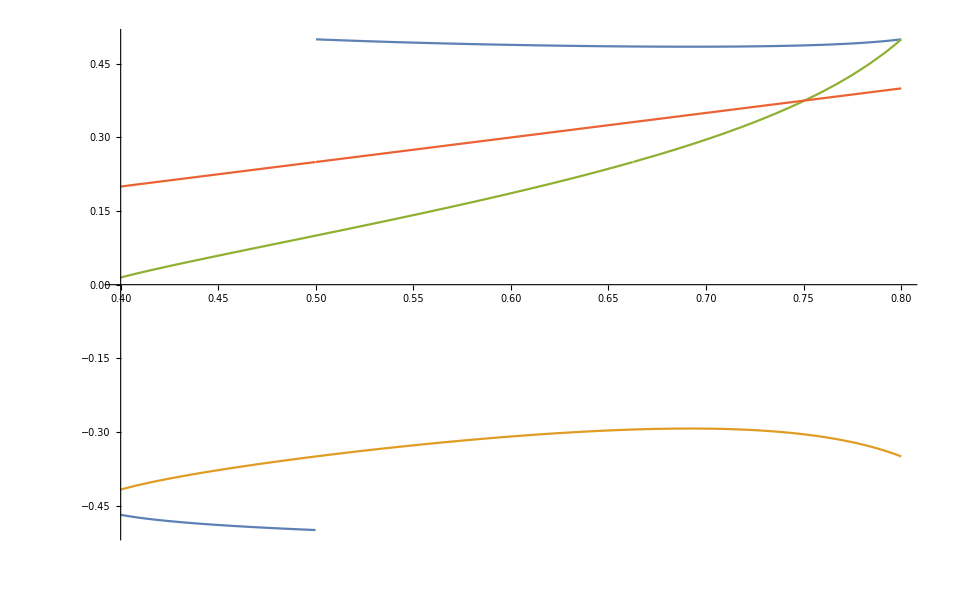

```mathematica
(* unimodularity constraint *)
x=Exp[I Pi γ];
Branch=1;
Subscript[χ, 1]=5-3 √5+4 √(5-2 √5)+(1+I) 1/x+Subscript[ζ, 2];
Subscript[χ, 2]=45-9 I-(17-7 I) √5-2 √(620-500 I-(285-234 I) √5)-(1+I) Subscript[χ, 1]/x;
Subscript[χ, 3]=10 I-10+(6-2 I) √5+4 √(10-10 ⅈ-(5-4 ⅈ) √5)+(1+I) Subscript[χ, 2]/x;
Subscript[χ, 4]=√5-1+I √2 √(5+√5)+(1+I) Subscript[χ, 3]/x;
Subscript[χ, 5]=(1+I) √(1-√5+Subscript[ζ, 4])-(1-I)( 2 x^2+Branch*Conjugate[√Subscript[χ, 4]])-x (1-4 I+√5+Subscript[ζ, 1]);
Subscript[χ, 6]=√5-1-I-√(5-2 √5)+(1- I) x;
y=1/4 Subscript[χ, 5]/Subscript[χ, 6];
z=x/(x-y)((1+I) (-1)^(4/5)-x-y-1+I);
u=I/z(x^2-z x + x y + y z)/(1+I-(-1)^(3/10)-(-1)^(4/5));
(* Arg or Abs ... *)
Plot[{Arg[y]/2./Pi,Arg[z]/2./Pi,Arg[u]/2./Pi,Arg[x]/2./Pi},{γ,2/5,4/5}](*Plot[{Arg[y]/2./Pi,Arg[z]/2./Pi,Arg[u]/2./Pi,Arg[x]/2./Pi},{γ,1,14/10}]*)
```

```mathematica
(* separator *)
```

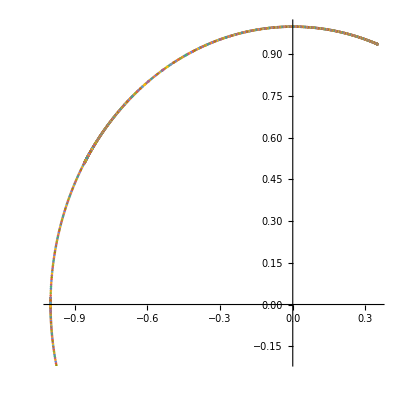

```mathematica
(* y, z and u as functions of x[γ] *)
x[γ_]:=Exp[I*Pi*γ];
Subscript[χ, 1][γ_]:=5-3 √5+4 √(5-2 √5)+(1+I) 1/x[γ]+Subscript[ζ, 2];
Subscript[χ, 2][γ_]:=45-9 I-(17-7 I) √5-2 √(620-500 I-(285-234 I) √5)-(1+I) (Subscript[χ, 1][γ])/x[γ];
Subscript[χ, 3][γ_]:=10 I-10+(6-2 I) √5+4 √(10-10 ⅈ-(5-4 ⅈ) √5)+(1+I) (Subscript[χ, 2][γ])/x[γ];
Subscript[χ, 4][γ_]:=√5-1+I √2 √(5+√5)+(1+I) (Subscript[χ, 3][γ])/x[γ];
Subscript[χ, 5][γ_]:=(1+I) √(1-√5+Subscript[ζ, 4])-(1-I)( 2 x[γ]^2+Conjugate[√(Subscript[χ, 4][γ])])-x[γ](1-4 I+√5+Subscript[ζ, 1]);
Subscript[χ, 6][γ_]:=√5-1-I-√(5-2 √5)+(1- I) x[γ];
y[γ_]:=1/4(Subscript[χ, 5][γ])/(Subscript[χ, 6][γ]);
z[γ_]:=x[γ]/(x[γ]-y[γ])((1+I) (-1)^(4/5)-x[γ]-y[γ]-1+I);
u[γ_]:=I/z[γ](x[γ]^2-z[γ] x[γ] + x[γ] y[γ] + y[γ] z[γ])/(1+I-(-1)^(3/10)-(-1)^(4/5));
ListPlot[Table[{{Re[y[γ]],Im[y[γ]]},{Re[u[γ]],Im[u[γ]]},{Re[z[γ]],Im[z[γ]]}},{γ,0.9700212764097545,1.413709525400110,0.001}],AspectRatio->1]
```

```mathematica
(* separator *)
```

```mathematica
(* try to extract {y, z, u} from T with q=-ix/z -- maybe y simplifies a bit... *)
(* T' T *)
```

```mathematica
({{8, 1+u+u/x+x-(ⅇ^((4 ⅈ π)/5) u)/y+ⅇ^((ⅈ π)/5) y-(ⅈ x)/z+(ⅈ u z)/x, 1-u+(ⅇ^((4 ⅈ π)/5) u)/x+ⅇ^((ⅈ π)/5) x-u/y+y+(ⅈ x)/z+(ⅈ u z)/x, 1+z-(u z)/x^2-(ⅈ z)/x-(ⅈ u z)/x-(ⅇ^((4 ⅈ π)/5) u z)/(x y)-(ⅇ^((ⅈ π)/5) y z)/x-(u z^2)/x^2, 1+ⅇ^((ⅈ π)/5) z-(ⅇ^((4 ⅈ π)/5) u z)/x^2+(ⅈ z)/x-(ⅈ u z)/x-(u z)/(x y)-(y z)/x+(u z^2)/x^2, 0, 0, 0}, {1+1/u+x/u+1/x-(ⅇ^(-(4 ⅈ π)/5) y)/u+ⅇ^(-(ⅈ π)/5) 1/y+(ⅈ z)/x-(ⅈ x)/(u z), 8, 0, 0, 0, 1-1/u+(ⅇ^((7 ⅈ π)/10) x)/u+ⅇ^((3 ⅈ π)/10) 1/x-(ⅈ y)/u-ⅈ 1/y+(ⅈ z)/x+(ⅈ x)/(u z), 1+1/u+(ⅈ x)/u-ⅈ 1/x+(ⅈ ⅇ^(-(4 ⅈ π)/5) y)/u+ⅈ ⅇ^(-(ⅈ π)/5) 1/y-(ⅈ z)/x+(ⅈ x)/(u z), 1-1/u+(ⅇ^(-(4 ⅈ π)/5) x)/u+ⅇ^(-(ⅈ π)/5) 1/x-y/u+1/y-(ⅈ z)/x-(ⅈ x)/(u z)}, {1-1/u+(ⅇ^(-(4 ⅈ π)/5) x)/u+ⅇ^(-(ⅈ π)/5) 1/x-y/u+1/y-(ⅈ z)/x-(ⅈ x)/(u z), 0, 8, 0, 0, 1+1/u+(ⅈ x)/u-ⅈ 1/x-(ⅇ^((7 ⅈ π)/10) y)/u+ⅇ^((3 ⅈ π)/10) 1/y-(ⅈ z)/x+(ⅈ x)/(u z), 1-1/u-(ⅈ ⅇ^(-(4 ⅈ π)/5) x)/u+ⅈ ⅇ^(-(ⅈ π)/5) 1/x-(ⅈ y)/u-ⅈ 1/y+(ⅈ z)/x+(ⅈ x)/(u z), 1+1/u+x/u+1/x-(ⅇ^(-(4 ⅈ π)/5) y)/u+ⅇ^(-(ⅈ π)/5) 1/y+(ⅈ z)/x-(ⅈ x)/(u z)}, {1+1/z+(ⅈ x)/z-x^2/(u z^2)-x^2/(u z)+(ⅈ x)/(u z)-(ⅇ^(-(4 ⅈ π)/5) x y)/(u z)-(ⅇ^(-(ⅈ π)/5) x)/(y z), 0, 0, 8, 0, 1+ⅇ^((3 ⅈ π)/10) 1/z+(ⅈ x)/z+x^2/(u z^2)-(ⅇ^((7 ⅈ π)/10) x^2)/(u z)-(ⅈ x)/(u z)-(ⅈ x y)/(u z)+(ⅈ x)/(y z), 1-ⅈ 1/z-(ⅈ x)/z-x^2/(u z^2)-(ⅈ x^2)/(u z)-(ⅈ x)/(u z)+(ⅈ ⅇ^(-(4 ⅈ π)/5) x y)/(u z)-(ⅈ ⅇ^(-(ⅈ π)/5) x)/(y z), 1+ⅇ^(-(ⅈ π)/5) 1/z-(ⅈ x)/z+x^2/(u z^2)-(ⅇ^(-(4 ⅈ π)/5) x^2)/(u z)+(ⅈ x)/(u z)-(x y)/(u z)-x/(y z)}, {1+ⅇ^(-(ⅈ π)/5) 1/z-(ⅈ x)/z+x^2/(u z^2)-(ⅇ^(-(4 ⅈ π)/5) x^2)/(u z)+(ⅈ x)/(u z)-(x y)/(u z)-x/(y z), 0, 0, 0, 8, 1-ⅈ 1/z-(ⅈ x)/z-x^2/(u z^2)-(ⅈ x^2)/(u z)-(ⅈ x)/(u z)-(ⅇ^((7 ⅈ π)/10) x y)/(u z)-(ⅇ^((3 ⅈ π)/10) x)/(y z), 1+ⅈ ⅇ^(-(ⅈ π)/5) 1/z+(ⅈ x)/z+x^2/(u z^2)+(ⅈ ⅇ^(-(4 ⅈ π)/5) x^2)/(u z)-(ⅈ x)/(u z)-(ⅈ x y)/(u z)+(ⅈ x)/(y z), 1+1/z+(ⅈ x)/z-x^2/(u z^2)-x^2/(u z)+(ⅈ x)/(u z)-(ⅇ^(-(4 ⅈ π)/5) x y)/(u z)-(ⅇ^(-(ⅈ π)/5) x)/(y z)}, {0, 1-u+(ⅇ^(-(7 ⅈ π)/10) u)/x+ⅇ^(-(3 ⅈ π)/10) x+(ⅈ u)/y+ⅈ y-(ⅈ x)/z-(ⅈ u z)/x, 1+u-(ⅈ u)/x+ⅈ x-(ⅇ^(-(7 ⅈ π)/10) u)/y+ⅇ^(-(3 ⅈ π)/10) y+(ⅈ x)/z-(ⅈ u z)/x, 1+ⅇ^(-(3 ⅈ π)/10) z-(ⅇ^(-(7 ⅈ π)/10) u z)/x^2-(ⅈ z)/x+(ⅈ u z)/x+(ⅈ u z)/(x y)-(ⅈ y z)/x+(u z^2)/x^2, 1+ⅈ z+(ⅈ u z)/x^2+(ⅈ z)/x+(ⅈ u z)/x-(ⅇ^(-(7 ⅈ π)/10) u z)/(x y)-(ⅇ^(-(3 ⅈ π)/10) y z)/x-(u z^2)/x^2, 8, 0, 0}, {0, 1+u-(ⅈ u)/x+ⅈ x-(ⅈ ⅇ^((4 ⅈ π)/5) u)/y-ⅈ ⅇ^((ⅈ π)/5) y+(ⅈ x)/z-(ⅈ u z)/x, 1-u+(ⅈ ⅇ^((4 ⅈ π)/5) u)/x-ⅈ ⅇ^((ⅈ π)/5) x+(ⅈ u)/y+ⅈ y-(ⅈ x)/z-(ⅈ u z)/x, 1+ⅈ z+(ⅈ u z)/x^2+(ⅈ z)/x+(ⅈ u z)/x-(ⅈ ⅇ^((4 ⅈ π)/5) u z)/(x y)+(ⅈ ⅇ^((ⅈ π)/5) y z)/x-(u z^2)/x^2, 1-ⅈ ⅇ^((ⅈ π)/5) z-(ⅈ ⅇ^((4 ⅈ π)/5) u z)/x^2-(ⅈ z)/x+(ⅈ u z)/x+(ⅈ u z)/(x y)-(ⅈ y z)/x+(u z^2)/x^2, 0, 8, 0}, {0, 1-u+(ⅇ^((4 ⅈ π)/5) u)/x+ⅇ^((ⅈ π)/5) x-u/y+y+(ⅈ x)/z+(ⅈ u z)/x, 1+u+u/x+x-(ⅇ^((4 ⅈ π)/5) u)/y+ⅇ^((ⅈ π)/5) y-(ⅈ x)/z+(ⅈ u z)/x, 1+ⅇ^((ⅈ π)/5) z-(ⅇ^((4 ⅈ π)/5) u z)/x^2+(ⅈ z)/x-(ⅈ u z)/x-(u z)/(x y)-(y z)/x+(u z^2)/x^2, 1+z-(u z)/x^2-(ⅈ z)/x-(ⅈ u z)/x-(ⅇ^((4 ⅈ π)/5) u z)/(x y)-(ⅇ^((ⅈ π)/5) y z)/x-(u z^2)/x^2, 0, 0, 8}})
```

```mathematica
Solve[1+u+u/x+x-(ⅇ^((4 ⅈ π)/5) u)/y+ⅇ^((ⅈ π)/5) y-(ⅈ x)/z+(ⅈ u z)/x==0,u]//FullSimplify
```

{{u→-(x y (z+(-1)^(1/5) y z+x (-ⅈ+z)))/(z (y+x (-(-1)^(4/5)+y)+ⅈ y z))}}

```mathematica
u=-(x y (z+(-1)^(1/5) y z+x (-ⅈ+z)))/(z (y+x (-(-1)^(4/5)+y)+ⅈ y z));
Solve[1+ⅈ ⅇ^(-(ⅈ π)/5) 1/z+(ⅈ x)/z+x^2/(u z^2)+(ⅈ ⅇ^(-(4 ⅈ π)/5) x^2)/(u z)-(ⅈ x)/(u z)-(ⅈ x y)/(u z)+(ⅈ x)/(y z)==0,z]//FullSimplify
```

{{z→1/(2 (1+(-1)^(4/5)) (x-y) y)((-1)^(1/10) y (1+(-1)^(1/5)+2 (-1)^(1/5) y)+x^2 (2 (-1)^(3/10)+(ⅈ+(-1)^(3/10)) y)+x ((-1)^(1/10)+(-1)^(3/10)+2 (ⅈ+(-1)^(1/10)) y+(ⅈ+(-1)^(3/10)) y^2)+√(-4 (-1)^(2/5) (-1+(-1)^(1/5))^2 x (x-y)^2 y+((-1)^(1/10) y (1+(-1)^(1/5)+2 (-1)^(1/5) y)+x^2 (2 (-1)^(3/10)+(ⅈ+(-1)^(3/10)) y)+x ((-1)^(1/10)+(-1)^(3/10)+2 (ⅈ+(-1)^(1/10)) y+(ⅈ+(-1)^(3/10)) y^2))^2))},{z→1/(2 (1+(-1)^(4/5)) (x-y) y)((-1)^(1/10) y (1+(-1)^(1/5)+2 (-1)^(1/5) y)+x^2 (2 (-1)^(3/10)+(ⅈ+(-1)^(3/10)) y)+x ((-1)^(1/10)+(-1)^(3/10)+2 (ⅈ+(-1)^(1/10)) y+(ⅈ+(-1)^(3/10)) y^2)-√(-4 (-1)^(2/5) (-1+(-1)^(1/5))^2 x (x-y)^2 y+((-1)^(1/10) y (1+(-1)^(1/5)+2 (-1)^(1/5) y)+x^2 (2 (-1)^(3/10)+(ⅈ+(-1)^(3/10)) y)+x ((-1)^(1/10)+(-1)^(3/10)+2 (ⅈ+(-1)^(1/10)) y+(ⅈ+(-1)^(3/10)) y^2))^2))}}

```mathematica
(* try to simplify z *)
k=(-1)^(1/10) y (1+(-1)^(1/5)+2 (-1)^(1/5) y)+x^2 (2 (-1)^(3/10)+(ⅈ+(-1)^(3/10)) y)+x ((-1)^(1/10)+(-1)^(3/10)+2 (ⅈ+(-1)^(1/10)) y+(ⅈ+(-1)^(3/10)) y^2);
```

```mathematica
1/(2 (1+(-1)^(4/5)) (x-y) y)(k+√(-4 (-1)^(2/5) (-1+(-1)^(1/5))^2 x (x-y)^2 y+(k)^2))//FullSimplify
```

1/(2 (1+(-1)^(4/5)) (x-y) y)((-1)^(1/10) y (1+(-1)^(1/5)+2 (-1)^(1/5) y)+x^2 (2 (-1)^(3/10)+(ⅈ+(-1)^(3/10)) y)+x ((-1)^(1/10)+(-1)^(3/10)+2 (ⅈ+(-1)^(1/10)) y+(ⅈ+(-1)^(3/10)) y^2)+√(-4 (-1)^(2/5) (-1+(-1)^(1/5))^2 x (x-y)^2 y+((-1)^(1/10) y (1+(-1)^(1/5)+2 (-1)^(1/5) y)+x^2 (2 (-1)^(3/10)+(ⅈ+(-1)^(3/10)) y)+x ((-1)^(1/10)+(-1)^(3/10)+2 (ⅈ+(-1)^(1/10)) y+(ⅈ+(-1)^(3/10)) y^2))^2))

```mathematica
k//FullSimplify
```

(-1)^(1/10) y (1+(-1)^(1/5)+2 (-1)^(1/5) y)+x^2 (2 (-1)^(3/10)+(ⅈ+(-1)^(3/10)) y)+x ((-1)^(1/10)+(-1)^(3/10)+2 (ⅈ+(-1)^(1/10)) y+(ⅈ+(-1)^(3/10)) y^2)

```mathematica
(x+y)((-1)^(1/10)+(-1)^(3/10))+(x^2+y^2)(2(-1)^(3/10))+2(ⅈ+(-1)^(1/10))x y+(ⅈ+(-1)^(3/10)) (x^2 y+x y^2)//FullSimplify
```

2 (ⅈ+(-1)^(1/10)) x y+((-1)^(1/10)+(-1)^(3/10)) (x+y)+(ⅈ+(-1)^(3/10)) x y (x+y)+2 (-1)^(3/10) (x^2+y^2)

```mathematica
Solve[1+1/u+x/u+1/x-(ⅇ^(-(4 ⅈ π)/5) y)/u+ⅇ^(-(ⅈ π)/5) 1/y+(ⅈ z)/x-(ⅈ x)/(u z)==0,y]//FullSimplify
```

{{y→((-1)^(4/5) ((1+u) x z+u (1+ⅈ z) z+x^2 (-ⅈ+z)+√(-4 u x^2 z^2+(-ⅈ x^2+(1+x) (u+x) z+ⅈ u z^2)^2)))/(2 x z)},{y→((-1)^(4/5) ((1+u) x z+u (1+ⅈ z) z+x^2 (-ⅈ+z)-√(-4 u x^2 z^2+(-ⅈ x^2+(1+x) (u+x) z+ⅈ u z^2)^2)))/(2 x z)}}

```mathematica
y=((-1)^(4/5) ((1+u) x z+u (1+ⅈ z) z+x^2 (-ⅈ+z)+√(-4 u x^2 z^2+(-ⅈ x^2+(1+x) (u+x) z+ⅈ u z^2)^2)))/(2 x z);
Solve[1-u+(ⅇ^((4 ⅈ π)/5) u)/x+ⅇ^((ⅈ π)/5) x-u/y+y+(ⅈ x)/z+(ⅈ u z)/x==0,z]
```

```mathematica
(* :/ *)
```